```mathematica
(*NSR_external_field_simulations_20250403: Simulating external field*)
(*spin_rotation_angle_20250115: attempt to add garnet and contaminant magnetizations before determining Tc*)
(*spin_rotation_angle_20250109: total magnetization reverted to conventional signs - below Tc, M > 0; adjusted contaminants accordingly; study various field coefficient dependence*)
(*spin_rotation_angle_20241030: Molecular field calculation added to notebook*)
(*spin_rotation_angle_20241025_2: Total magnetization negated to match direction taken as positive*)
(*spin_rotation_angle_20241025: added perovskite and hematite contributions*)
(*spin_rotation_angle_20240920: sample geometry matches 2024 arXiv preprint*)
```

```mathematica
(*Magnetization from molecular field theory*)
Clear[dT,Tm,NA,muB,rho,A,kB,h,naa,nad,ndd,nac,ncc,ndd,Jc,Sc,Lc,Ja,Sa,La,Jd,Sd,Ld,gamma,Lcpp,Jcpp,d,gc,gcs,ga,gd,gcpp,muc0,mua0,mud0,xc,xa,xd,bjc,bja,bjd,rtr,n,muct,muat,mudt,must,i,tc,muctc,muatc,mudtc,sctc,sxtc,mutp,musti,imust,mustp,imustp,Treq,lTreq,Mreq,mutp,garPct,perovPct,hemPct];

(*input*)
samples={"2023","2024","prelim","spring8","powder"};
garPcts={0.887,0.956,0.51,0.908,0.908};
perovPcts={0.086,0.0047,0.438,0.042,0.072};
hemPcts={0.027,0.039,0.06,0.05,0.02};

(*masses and volumes are not exact; total number of molecules will not be correct, but ratios will be*)
masses={7.973 10^-3,7.973 10^-3,0.088*10^(-3),7.973 10^-3,0.0534*10^(-3)};
volumes={ 2.098 10^-6 ,2.098 10^-6, 2 10^-8,2.098 10^-6};

(*Set the sample you want to test:*)
i=5;
(*sample purity*)
garPct=garPcts[[i]];
perovPct=perovPcts[[i]];
hemPct=hemPcts[[i]];
mass=masses[[i]]; 

(*Temperature parameters*)
dT=1.;   (*increment, K*)
Tm=400;  (*maximum, K*)

(*physical constants*)
NA=6.02 10^23;(*Avogadro*)
muB=9.274 10^-21;(*Bohr magneton,erg/G*)
kB=1.381 10^-16 ;(*Boltzmann, erg/K*)

(*field coefficients in mol/cc*)
naa=-65.0;  (*octahedral-octahedral[Dionne71]*)
nad=97.0;     (*octahedral-tetrahedral[Dionne71]*)
ndd=-30.4;(*tetrahedral-tetrahedral[Dionne71]*)

nac=-4.2 ;(*octahedral-dodecahedral[Dionne79, Dionne09]*)
ncc=0.;   (*dodecahedral-dodecahedral[Dionne79, Dionne09]*)
ncd=6.5;  (*dodecahedral-tetrahedral[Dionne79, Dionne09]*)

(*angular momenta in hbar[Dionne09]*)
gamma=0.32; (*quenching factor*)

(*gamma=0.25;(*quenching factor to yield Tc = 250 K, empirical*)*)
Sc=3;(*Tb spin*)
Lc=gamma 3;(*Tb orbit*)
Jc=Lc+Sc;(*Tb total*)

Sa=5/2;(*Fe spin*)
Sd=5/2;(*Fe spin*)

(*calculations*)
(*g-factors*)
gc=1+(Jc (Jc+1)+Sc (Sc+1)-Lc (Lc+1))/(2 Jc (Jc+1)); (*rare earth*)
gcs=1+(Sc (Sc+1)-Lc (Lc+1))/(Jc (Jc+1));                            (*rare earth spin*)
ga=2.; (*Fe,all spin*)
gd=2.; (*Fe,all spin*)

(*initial magnetization,T=0*)
muc0=3. gc Jc muB NA;
mua0=2. ga Sa muB NA;
mud0=3. gd Sd muB NA;

mustList={};
fields={};
sxList={};
For[j=0,j<15,j++,

(*molecular fields*)
field=j*5000;
AppendTo[fields,field];
xc=(Jc gc muB)/(kB dT (n+1)) (ncc muc[n]+nac mua[n]+ncd mud[n]-2field);
xa=(Sa ga muB)/(kB dT (n+1)) (naa mua[n]+nac muc[n]+nad mud[n]-2field);
xd=(Sd gd muB)/(kB dT (n+1)) (ndd mud[n]+ncd muc[n]+nad mua[n]+2field);

(*Brillouin functions*)
bjc=((2 Jc+1)/(2 Jc)) Coth[(2 Jc+1) xc/(2 Jc)]-(1/(2 Jc)) Coth[xc/(2 Jc)];
bja=((2 Sa+1)/(2 Sa)) Coth[(2 Sa+1) xa/(2 Sa)]-(1/(2 Sa)) Coth[xa/(2 Sa)];
bjd=((2 Sd+1)/(2 Sd)) Coth[(2 Sd+1) xd/(2 Sd)]-(1/(2 Sd)) Coth[xd/(2 Sd)];

(*solve recurrence equations for moments at successive T*)rtr=RecurrenceTable[{muc[n+1]==muc0 bjc,mua[n+1]==mua0 bja,mud[n+1]==mud0 bjd,muc[0]==muc0,mua[0]==mua0,mud[0]==mud0},{muc,mua,mud},{n,0,Tm}];

(*moment vs.T lists*)
muct=Table[{i dT,rtr[[i+1,1]]/(muB NA)},{i,1,Tm}];
muat=Table[{i dT,rtr[[i+1,2]]/(muB NA)},{i,1,Tm}];
mudt=Table[{i dT,-rtr[[i+1,3]]/(muB NA)},{i,1,Tm}];
must=Table[{i dT,Abs[rtr[[i+1,1]]+rtr[[i+1,2]]-rtr[[i+1,3]]]/(muB NA)},{i,1,Tm}];
imuct=Interpolation[muct];
imuat=Interpolation[muat];
imudt=Interpolation[mudt];

(*interpolation*)musti=Table[{i dT,(rtr[[i+1,1]]+rtr[[i+1,2]]-rtr[[i+1,3]])/(muB NA)},{i,1,Tm}];
imust=Interpolation[musti];
(*garnet powder tc*)
AppendTo[mustList,imust[266+45]];

(*revised TC: get moment as function of T, then find root*)
tc=FindRoot[imust[T]==0.,{T,100.}][[1,2]];

(*contribution of rare earth at Tc*)
sxtc=imuct[tc]*(gcs/gc)+imuat[tc]+imudt[tc];

(*total moment and magnetization*)
Clear[NA,u,muBSI,mTb,mFe,mO,mTbIG,perovMomenti,iperovMoment,hemMomentt,hemMomentm,hemMomenti,ihemMoment,mPerov,mHemat,tct,s0,BT,d,TC];
(*data*)
NA=6.022*10^23;
u=1.66 10^-27;(*amu, kg*)
muBSI = (1 10^-3)muB;(*Bohr Magneton, J/T*)
mTb = 158.93;(*Tb mass, u*)
mFe = 55.854;(*Fe mass, u*)
mO=15.999;(*O mass, u*)

s0=0.039;(*zero-T perovskite moment [Treves1965],uB/molecule*)
BT=0.95;(*pure S=5/2 ferromagnet T-dependence, approx.[Dionne2009]*)
d=0.32;(*Fe-Tb interaction parameter [Treves1965]]*)
TC = 650.;(*perovskite Curie T [Treves1965], K]*)
(*calculations*)
(*perovMoment ={0.075,.072,.070,.067}; (*uB/molecule for perovskite [Park2008], this was ZFC at 300Oe applied field so may not be valid*)*)
(*s0 (interpretation 1 of old data) [Treves1965]*)
perovMomenti=Table[{i dT,(-s0 BT (1.+d TC/i))},{i,1,Tm}];(*perovskite moment, uB/molecule; convention is negative*)
iperovMoment=Interpolation[perovMomenti];(*interpolated perovskite moment*)
hemMomentt={1.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.,210.,220.,230.,240.,250.,260.,270.,280.,290.,300.};(*hematite moment T data [Andre-Filho2014]]*)
hemMomentm=-(159.69/NA*1.078*10^20){0.019,0.019,0.019,0.019,0.019,0.019,0.0191,0.0192,0.0193,0.0194,0.0195,0.0196,0.0197,0.0198,0.0199,0.02,0.0201,0.0202,0.0205,0.021,0.0215,0.022,0.023,0.025,0.03,0.04,0.06,0.09,.11,.12,.123};(*hematite moment data [Andre-Filho2014],from emu/g to uB/molecule, convention is negative*)
hemMomenti=Table[{hemMomentt[[i]],hemMomentm[[i]]},{i,1,31}];(*hematite moment data [Andre-Filho2014]]*)
ihemMoment=Interpolation[hemMomenti];(*interpolated hematite moment*)
mTbIG = 3.0 mTb+5.0 mFe+12.0 mO;(*TbIG mass, u*)
mPerov = mTb + mFe + 3.0 mO;(*perovskite mass, u*)
mHemat = 2.0 mFe + 3.0 mO;(*hematite mass, u*)
ng=garPct mass /(u mTbIG);(*molecules of garnet*)
np= perovPct mass/(u mPerov);(*molecules of perovskite*)
nh = hemPct mass /(u mHemat); (*molecules of hematite*)
nt=ng+np+nh;(*total molecules*)
tct=FindRoot[(muBSI ng imust[T]+muBSI  np iperovMoment[T]+muBSI  nh ihemMoment[T])==0.,{T,100.}][[1,2]];(*total TC: compute total moment as function of T, then find root*)

Clear[sx45];
(*spin density at sample Tc and sample tc + 45*)

(*1% uncertainty in coeffs*)

tct=252;(*keep temp consistent*)
sx45=Around[imuct[tct+45]*(gcs/gc)+imuat[tct+45]+imudt[tct+45],0.01*(imuct[tct+45]*(gcs/gc)+imuat[tct+45]+imudt[tct+45])];

AppendTo[sxList,sx45];

]

(*Now, adjust those values for purity*)
ng=garPct mass/(u mTbIG);(*molecules of garnet*)
np = perovPct mass/(u mPerov);(*molecules of perovskite*)
nh = hemPct mass/(u mHemat); (*molecules of hematite*)
nt=ng+np+nh;

If[samples[[i]]=="prelim",
(*Converting model spin excess to what would be expected from spring 8 prelim measurement*)

(*spontaneous to remanent ratio, still needed when magnetized*)

garspin25T = sxList[[6]];
perovmoment25T =Around[-0.0625,0.0015]+1/2*((Around[-35,0.5]-Around[32.5,0.5])*10^-7)*25000;(*Treves65*)
hemsusc=0.4; (*m^3/kg 10^-6*)
(*unmilled hem moment goes up to about 0.5 emu/g at 25000 Oe*)

hemmoment25T = -(159.69/NA*1.078*10^20)*0.5;
totalspin25T=garspin25T*ng/nt+hemmoment25T*nh/nt+perovmoment25T*np/nt;
(*Comparison to 0.92 prediction:*)
Print["Total spin density at 2.5T at room temp for small sample: ",totalspin25T];
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

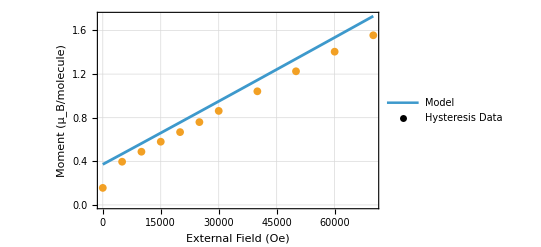

```mathematica
(*7T hysteresis from 9Dec2024*)
hysteresisFields={0,5000,10000,15000,20000,25000,30000,40000,50000,60000,70000};
hysteresisData={0.0426,0.108,0.133,0.158,0.182,0.207,0.235,0.284,0.334,0.383,0.424}*3.67;

(*perovskite moment as function of field*)
perovMomentField=-0.0625+1/2*(-35-32.5)*10^-7*fields*np/nt;

externalFieldGarnetModel=-mustList*ng/nt;

combinedPlot=Show[ListPlot[{Transpose[{fields,externalFieldGarnetModel-perovMomentField}],Transpose[{hysteresisFields,hysteresisData}]},Joined->{True,False},PlotMarkers->{None,{"●",8}},Frame->True,FrameLabel->{Style["External Field (Oe)",Black,16],Style["Moment (μ_B/molecule)",Black,16]},FrameTicksStyle->Directive[FontSize->12,Black],PlotLegends->Placed[{"Model","Hysteresis Data"},{0.8,0.15}],PlotStyle->{Thickness[0.005]},GridLines->Automatic,ImageSize->400,BaseStyle->{FontColor->Black},PlotStyle->Black]]
```